```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

### Definitions

```mathematica
αcont=SetPrecision[{0.5137193759431391,0.0024666827878353577},500]; 
σcont=SetPrecision[{0.16955497884544793,0.0008581023195660334},500];
ccont=SetPrecision[{-0.15956635071361625,0.0024752900407607015},500];
```

```mathematica
Πpar[θ_,v_,mD_]:=SetPrecision[mD^2/2((2-2 v^2-v^4 Cos[θ]^2 Sin[θ]^2)/((1-v^2 Sin[θ]^2)^2)-((2+v^2 Sin[θ]^2)(1-v^2)v Cos[θ])/(2(1-v^2 Sin[θ]^2)^(5/2))Log[(v Cos[θ]+√(1-v^2 Sin[θ]^2))/(v Cos[θ]-√(1-v^2 Sin[θ]^2))]),200];
Πper[θ_,β_,v_,mD_]:=SetPrecision[mD^2/2((2-2 v^2-v^4 Cos[β]^2 Sin[θ]^2(1-Cos[β]^2 Sin[θ]^2))/((1-v^2+v^2 Cos[β]^2 Sin[θ]^2)^2)-((2+v^2-v^2 Cos[β]^2 Sin[θ]^2)(1-v^2)v Cos[β]Sin[θ])/(2(1-v^2+v^2 Cos[β]^2 Sin[θ]^2)^2)Log[(v Cos[β]Sin[θ]+√(1-v^2+v^2 Cos[β]^2 Sin[θ]^2))/(v Cos[β]Sin[θ]-√(1-v^2+v^2 Cos[β]^2 Sin[θ]^2))]),100];
```

## Real part

Coulomb

```mathematica
ReVcpar[r_,mD_,v_,α_]:=-α/r+α NIntegrate[Sin[θ] √Re[Πpar[θ,v,mD]] Exp[-√Re[Πpar[θ,v,mD]]r Cos[θ]],{θ,0,π/2},MaxRecursion->20];
```

#### Check that ReVcpar[m -> 0] -> -α/r

```mathematica
Limit[Πpar[θ,v,mD],mD->0]
```

0

#### Check that this results replicates original 3d integral (i.e. that contour integral was performed correctly)

```mathematica
ReVcparcheck[r_,mD_,v_,α_]:=-α/π Quiet[ NIntegrate[p^2 Sin[θ] Exp[ⅈ r p Cos[θ]]/(p^2+Re[Πpar[θ,v,mD]]),{p,0,∞},{θ,0,π}]];
```

```mathematica
Quiet[ParallelTable[{a,ReVcparcheck[10^a,15/100,1/2,αcont[[1]]]},{a,-10,10}]]
```

{-8.96683×10^7+6.54976×10^-6 ⅈ,-1.11816×10^9+1.18909×10^-6 ⅈ,-3.00294×10^7+93.4647 ⅈ,-5.39615×10^6+0.170817 ⅈ,-509106.+0.1095 ⅈ,-51373.7+0.001022 ⅈ,-5137.82+3.1147×10^-9 ⅈ,-513.644-1.61681×10^-11 ⅈ,-51.2967+2.06747×10^-11 ⅈ,-5.06395-2.5794×10^-13 ⅈ,-0.442072+6.4202×10^-11 ⅈ,-0.00902205+1.28521×10^-10 ⅈ,0.0000404635+3.77887×10^-11 ⅈ,-2.59617-0.492158 ⅈ,-0.150626+1.00098 ⅈ,3.23879×10^-6-6.37063×10^-15 ⅈ,2.54816×10^-7+3.52873×10^-16 ⅈ,7.62311×10^-9+7.74498×10^-18 ⅈ,9.50127×10^-11+8.91854×10^-19 ⅈ,9.74076×10^-13+8.14327×10^-20 ⅈ,9.76772×10^-15+7.10716×10^-21 ⅈ}

```mathematica
Table[{a,ReVcpar[10^a,15/100,1/2,αcont[[1]]]},{a,-10,10}]
```

{{-10,-5.13719×10^9},{-9,-5.13719×10^8},{-8,-5.13719×10^7},{-7,-5.13719×10^6},{-6,-513719.},{-5,-51371.9},{-4,-5137.12},{-3,-513.643},{-2,-51.2956},{-1,-5.0613},{0,-0.442072},{1,-0.00902193},{2,0.0000404636},{3,3.71289×10^-8},{4,3.71022×10^-11},{5,3.70965×10^-14},{6,1.86114×10^-15},{7,-5.39697×10^-18},{8,-5.55562×10^-18},{9,-5.45194×10^-18},{10,-5.44838×10^-18}}

#### Check that ReVcpar[v -> 0] -> screened Coulomb

```mathematica
Block[{r=105,mD=0.15},ReVcpar[r,mD,0,αcont[[1]]]-(-αcont[[1]] Exp[- mD r]/r)]
```

1.26946×10^-17

#### Check asymptotic values

```mathematica
ReVcpar[10^-10,0.15,0.1,αcont[[1]]]
```

-5.13719×10^9

```mathematica
ReVcpar[10^10,0.15,0.1,αcont[[1]]]
```

-4.74221×10^-18

```mathematica
ReVcpar[10^-10,0.15,0.9,αcont[[1]]]
```

-5.13719×10^9+0.0201829 ⅈ

```mathematica
ReVcpar[10^10,0.15,0.9,αcont[[1]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000885249+0.000437269 ⅈ and 0.00790474 for the integral and error estimates.

-0.00045477+0.000224634 ⅈ

#### Plots

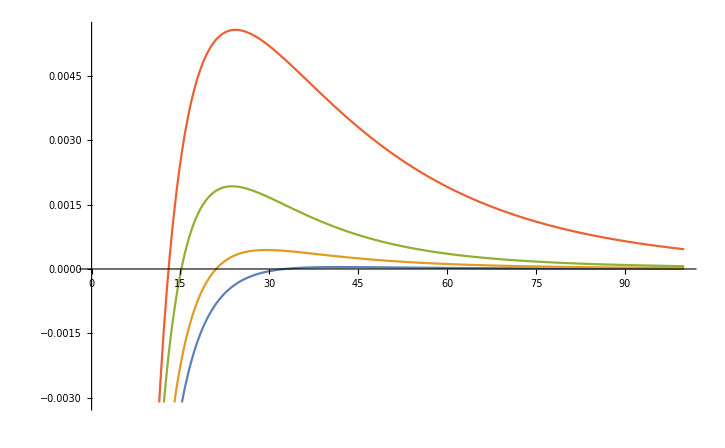

```mathematica
Plot[{ReVcpar[r,0.15,0.2,αcont[[1]]],ReVcpar[r,0.15,0.4,αcont[[1]]],ReVcpar[r,0.15,0.6,αcont[[1]]],ReVcpar[r,0.15,0.8,αcont[[1]]]},{r,0,100}]
```

#### Needs addressing

```mathematica
ReVcpar[10,0.15,0.9,αcont[[1]]](*IMAGINARY PART NON-ZERO??? take a look at roots of self-energy again*)
```

-0.00590861+0.0174719 ⅈ

String

We employ the BCs: ReVs'(r)|r→∞=0 (this was also true of the Coulomb solution at v=0 but we didn't impose it, in fact we had ReVs(r)|r→∞=0 but then added arbitrary constants so the condition here is equivalent) AND ReVs(r)|r→0=0 OR ReVs'(r)|r→0=0 (in order to employ the Wronskian method we need to choose one of the real/imag parts of ParabolicCylinderD[-1/2,ⅈ √2(mD^2 σ/α)^(1/4)r] to be our other unique solution, both blow up as r→∞, the real part is flat and non-zero around r=0 while the imaginary part the other way round)

### Define g function (RHS of ODE)

```mathematica
(*definition*)
```

```mathematica
gReAn[r_,mD_,v_,α_]:=2 α/r NIntegrate[Cos[θ]Sin[θ]Re[Πpar[θ,v,mD]]Exp[-r Cos[θ] √Re[Πpar[θ,v,mD]]],{θ,0,π/2}]-α NIntegrate[Cos[θ]^2 Sin[θ] Re[Πpar[θ,v,mD]]^(3/2)Exp[-r Cos[θ] √Re[Πpar[θ,v,mD]]],{θ,0,π/2}]+mD^2 ReVcpar[r,mD,v,α];
```

#### Check that gReAn[v -> 0] ->DiracDelta[r]

```mathematica
Quiet[ParallelTable[{a,gReAn[10^a,15/100,0,αcont[[1]]]},{a,-30,5}]]
```

{{-30,6.59707×10^12},{-29,6.87195×10^11},{-28,6.87195×10^10},{-27,6.44245×10^9},{-26,8.05306×10^8},{-25,6.71089×10^7},{-24,6.29146×10^6},{-23,655360.},{-22,65536.},{-21,6144.},{-20,512.},{-19,64.},{-18,8.},{-17,0.75},{-16,0.0625},{-15,0.00390625},{-14,0.000732422},{-13,0.0000610352},{-12,7.62939×10^-6},{-11,7.15256×10^-7},{-10,5.96046×10^-8},{-9,5.58794×10^-9},{-8,4.65661×10^-10},{-7,5.82077×10^-11},{-6,5.45697×10^-12},{-5,4.54747×10^-13},{-4,2.84217×10^-14},{-3,7.10543×10^-15},{-2,6.66134×10^-16},{-1,8.32667×10^-17},{0,5.20417×10^-18},{1,9.37835×10^-18},{2,3.12216×10^-19},{3,-1.29273×10^-19},{4,-1.47587×10^-19},{5,-9.99605×10^-20}}

## Construct ReVs

#### Wronskian

```mathematica
N[Wronskian[{ParabolicCylinderD[-1/2,√2 x μ],ParabolicCylinderD[-1/2,ⅈ √2 x μ]},x]/.{x->10^7,μ->5}]
```

5.-5. ⅈ

### Solution

```mathematica
ReVs[r_,mD_,α_,σ_]:=-Re[ParabolicCylinderD[-1/2,ⅈ √2(mD^2 σ/α)^(1/4) r]]Quiet[NIntegrate[(ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4) s] s^2 gReAnInter[s])/((mD^2 σ/α)^(1/4)),{s,r,10^5},MaxRecursion->20,WorkingPrecision->10]]-ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)r]Quiet[NIntegrate[(Re[ParabolicCylinderD[-1/2,ⅈ √2(mD^2 σ/α)^(1/4) s]] s^2 gReAnInter[s])/((mD^2 σ/α)^(1/4)),{s,0,r},MaxRecursion->20,WorkingPrecision->10]];
```

#### Plots for v=0.5,mD=0.15

```mathematica
(*evaluation for these parameters*)
```

```mathematica
Block[{v=1/2,mD=15/100,α=αcont[[1]]},gReAnTab=Join[ParallelTable[{r,gReAn[r,mD,v,α]},{r,10^-10,10^-5,10^-10}],ParallelTable[{r,gReAn[r,mD,v,α]},{r,2 10^-5,10^-1,10^-5}],ParallelTable[{r,gReAn[r,mD,v,α]},{r,2 10^-1,100,10^-1}],ParallelTable[{r,gReAn[r,mD,v,α]},{r,101,10^5,1}]]]//AbsoluteTiming;
```

```mathematica
gReAnInter=Interpolation[gReAnTab];
```

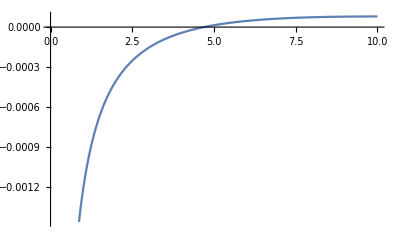

```mathematica
Plot[gReAnInter[r],{r,10^-10,10}]
```

```mathematica
ReVsTab=ParallelTable[{r,ReVs[r,15/100,αcont[[1]],σcont[[1]]]},{r,10^-10,100,1/10}];
```

```mathematica
ReVsInter=Interpolation[ReVsTab];
```

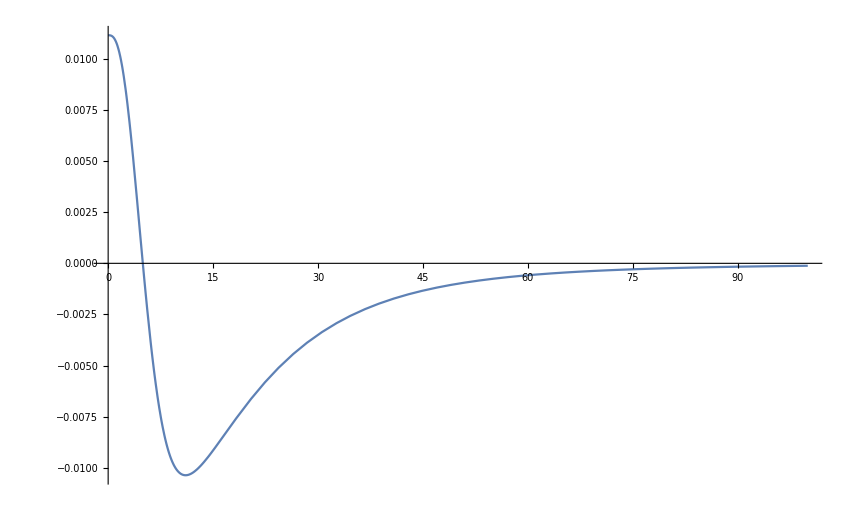

```mathematica
Plot[ReVsInter[r],{r,10^-10,100}]
```

#### Check that ReVs[m -> 0] ->σr

```mathematica
Block[{v=1/2,mD=1/1000,α=αcont[[1]]},gReAnTab=Join[ParallelTable[{r,gReAn[r,mD,v,α]},{r,10^-10,10^-5,10^-10}],ParallelTable[{r,gReAn[r,mD,v,α]},{r,2 10^-5,10^-1,10^-5}],ParallelTable[{r,gReAn[r,mD,v,α]},{r,2 10^-1,100,10^-1}],ParallelTable[{r,gReAn[r,mD,v,α]},{r,101,10^5,1}]]]//AbsoluteTiming;
```

```mathematica
gReAnInter=Interpolation[gReAnTab];
```

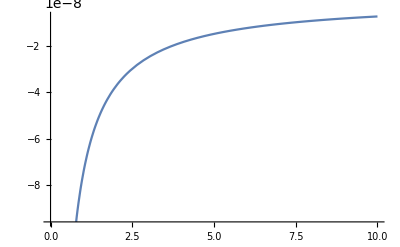

```mathematica
Plot[gReAnInter[r],{r,10^-10,10}]
```

```mathematica
ReVsTab=ParallelTable[{r,ReVs[r,15/100,αcont[[1]],σcont[[1]]]},{r,10^-10,100,1/10}];
```

```mathematica
ReVsInter=Interpolation[ReVsTab];
```

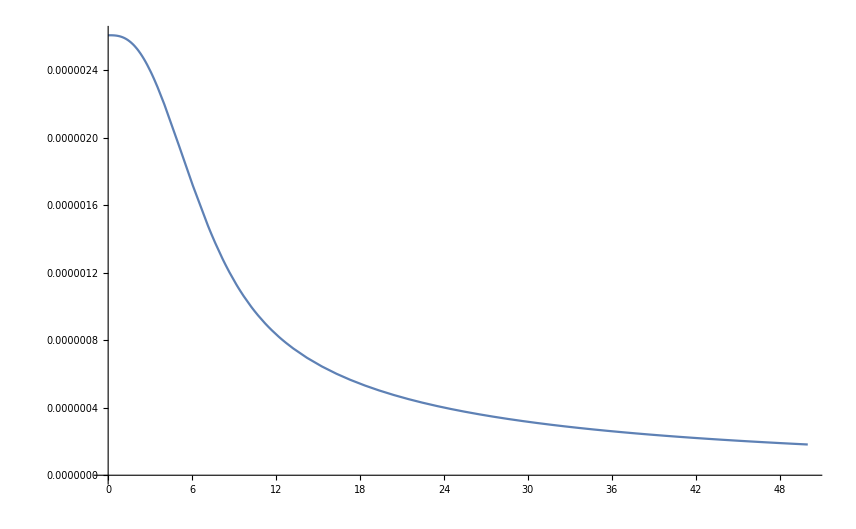

```mathematica
Plot[ReVsInter[r],{r,10^-10,50}]
```

#### Check that ReVs[v -> 0] ->ReVsold

```mathematica
ReVsold[r_,mD_,α_,σ_]:=Gamma[1/4]/(2^(3/4)√π)σ/((mD^2 σ/α)^(1/4))ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)r]+Gamma[1/4]/(2 Gamma[3/4])σ/((mD^2 σ/α)^(1/4));
```

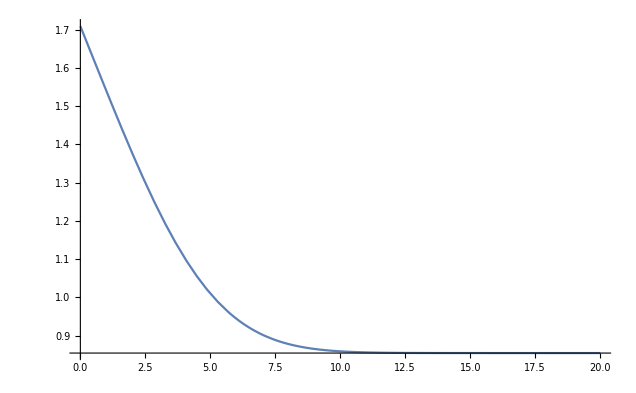

```mathematica
Plot[ReVsold[r,15/100,αcont[[1]],σcont[[1]]],{r,0,20},PlotRange->All]
```

## Imaginary part

Coulomb

```mathematica
ImVcpar[r_,mD_,v_,α_,T_]:=α T mD^2(1-v^2)^(3/2)NIntegrate[Re[Sin[θ](2+v^2 Sin[θ]^2)/(2(1+v^2 Sin[θ]^2)^(5/2))1/(ⅈ Im[Πpar[θ,v,mD]])(Sinh[r Cos[θ] √Πpar[θ,v,mD]]SinhIntegral[r Cos[θ] √Πpar[θ,v,mD]]-Cosh[r Cos[θ] √Πpar[θ,v,mD]]CoshIntegral[r Cos[θ] √Πpar[θ,v,mD]]-Sinh[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]SinhIntegral[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]+Cosh[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]CoshIntegral[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]])],{θ,0,π/2},Method->"GlobalAdaptive",WorkingPrecision->11,AccuracyGoal->11];
```

#### Check that ImVcpar[m -> 0] ->0

```mathematica
Block[{r=10^1,mD=10^-20,v=1/2},ImVcpar[r,mD,v,1,1]]
```

-0.47521547013

```mathematica
(*also the case for v=0 where we add in the 1- to the ϕ in order to compensate*)
```

#### Check that this results replicates original 3d integral (i.e. that contour integral was performed correctly)

```mathematica
ImVcparcheck[r_,mD_,v_,α_,T_]:=-α T mD^2(1-v^2)^(3/2)NIntegrate[Sin[θ](2+v^2 Sin[θ]^2)/(2 (1+v^2 Sin[θ]^2)^(5/2))(p Exp[ⅈ p r Cos[θ]])/((p^2+Πpar[θ,v,mD])(p^2+Conjugate[Πpar[θ,v,mD]])),{p,0,∞},{θ,0,π}]
```

```mathematica
Quiet[ParallelTable[{a,ImVcparcheck[10^a,15/100,1/2,αcont[[1]],155/1000]},{a,-10,10}]]
```

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

$Aborted

```mathematica
ImVcparcheck[10^1,15/100,1/2,αcont[[1]],155/1000]
```

-0.0169343-6.68507×10^-13 ⅈ

```mathematica
Table[{a,ImVcpar[10^a,15/100,1/2,αcont[[1]],155/1000]},{a,-10,10}]
```

{{-10,-0.037839746187},{-9,-0.037839746187},{-8,-0.037839746187},{-7,-0.037839746187},{-6,-0.037839746187},{-5,-0.037839746186},{-4,-0.037839746148},{-3,-0.037839743063},{-2,-0.037839508472},{-1,-0.03782344325},{0,-0.03695447438},{1,-0.016934290667},{2,-0.00012591221651},{3,-0.000017006509386},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0}}

#### Check that ImVcpar[v -> 0] ->ϕ

```mathematica
ImVc0[r_,mD_,α_,T_]:=-α T Quiet[2NIntegrate[z/((z^2+1)^2)Sinc[mD r z],{z,0,∞}]];
```

```mathematica
Block[{r=10,mD=15/100,α=αcont[[1]],T=155/1000},ImVcpar[r,mD,10^-5,α,T]-ImVc0[r,mD,α,T]]
```

-4.4581×10^-7

#### Check asymptotic values

```mathematica
ImVcpar[10^-10,15/100,1/10,αcont[[1]],155/100]
```

-0.77195164568

```mathematica
ImVcpar[10^10,15/100,1/10,αcont[[1]],155/100]
```

0

```mathematica
ImVcpar[10^-10,15/100,9/10,αcont[[1]],155/100]
```

-0.075459276822

```mathematica
ImVcpar[10^10,15/100,9/10,αcont[[1]],155/100]
```

0

#### Plots

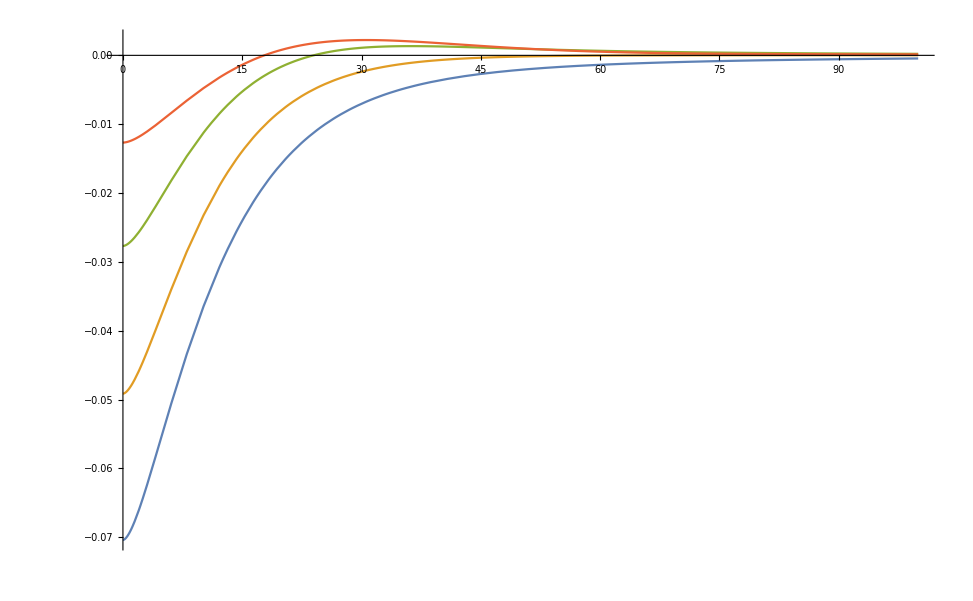

```mathematica
Quiet[Plot[{ImVcpar[r,15/100,2/10,αcont[[1]],155/1000],ImVcpar[r,15/100,4/10,αcont[[1]],155/1000],ImVcpar[r,15/100,6/10,αcont[[1]],155/1000],ImVcpar[r,15/100,8/10,αcont[[1]],155/1000]},{r,0,100},PlotRange->All]]
```

String

We employ the BCs: ReVs'(r)|r→∞=0 and ReVs'(r)|r→0=0

### Define g function (RHS of ODE)

```mathematica
(*definition*)
```

```mathematica
gImAn[r_,mD_,v_,α_,T_]:=α T mD^2(1-v^2)^(3/2)1/r NIntegrate[Re[Cos[θ] Sin[θ](2+v^2 Sin[θ]^2)/(2(1+v^2 Sin[θ]^2)^(5/2))1/(ⅈ Im[Πpar[θ,v,mD]])(2 √Conjugate[Πpar[θ,v,mD]] (-CoshIntegral[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]] Sinh[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]]+Cosh[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]] SinhIntegral[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]])+r Conjugate[Πpar[θ,v,mD]] Cos[θ] (-Cosh[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]] CoshIntegral[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]]+Sinh[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]] SinhIntegral[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]])+√Πpar[θ,v,mD] (CoshIntegral[r Cos[θ] √Πpar[θ,v,mD]] (r Cos[θ] Cosh[r Cos[θ] √Πpar[θ,v,mD]] √Πpar[θ,v,mD]+2 Sinh[r Cos[θ] √Πpar[θ,v,mD]])-(2 Cosh[r Cos[θ] √Πpar[θ,v,mD]]+r Cos[θ] √Πpar[θ,v,mD] Sinh[r Cos[θ] √Πpar[θ,v,mD]]) SinhIntegral[r Cos[θ] √Πpar[θ,v,mD]]))],{θ,0,π/2},Method->"GlobalAdaptive",WorkingPrecision->20,MaxRecursion->20,PrecisionGoal->10]+mD^2 ImVcpar[r,mD,v,α,T];
```

```mathematica
gImAnInterOne[r1_,mD1_,v1_,α1_,T1_]:=Block[{r=r1,mD=mD1,v=v1,α=α1,T=T1,inter,tab},tab=SetPrecision[ParallelTable[{θ,Re[Cos[θ] Sin[θ](2+v^2 Sin[θ]^2)/(2(1+v^2 Sin[θ]^2)^(5/2))1/(ⅈ Im[Πpar[θ,v,mD]])(2 √Conjugate[Πpar[θ,v,mD]] (-CoshIntegral[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]] Sinh[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]]+Cosh[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]] SinhIntegral[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]])+r Conjugate[Πpar[θ,v,mD]] Cos[θ] (-Cosh[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]] CoshIntegral[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]]+Sinh[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]] SinhIntegral[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]])+√Πpar[θ,v,mD] (CoshIntegral[r Cos[θ] √Πpar[θ,v,mD]] (r Cos[θ] Cosh[r Cos[θ] √Πpar[θ,v,mD]] √Πpar[θ,v,mD]+2 Sinh[r Cos[θ] √Πpar[θ,v,mD]])-(2 Cosh[r Cos[θ] √Πpar[θ,v,mD]]+r Cos[θ] √Πpar[θ,v,mD] Sinh[r Cos[θ] √Πpar[θ,v,mD]]) SinhIntegral[r Cos[θ] √Πpar[θ,v,mD]]))]},{θ,0,π/2,1/10000}],100];
inter=Interpolation[tab];
Return[α T mD^2(1-v^2)^(3/2)1/r NIntegrate[inter[x],{x,0,π/2}]+mD^2 ImVcpar[r,mD,v,α,T]]];
```

#### Check that gReAn[v -> 0] ->g_old

```mathematica
gold[r_,mD_,α_,T_]:=-α T mD^2 Quiet[2NIntegrate[p/(p^2+1)Sinc[p mD r],{p,0,∞}]];
```

```mathematica
Quiet[ParallelTable[{a,gold[10^a,15/100,αcont[[1]],155/1000]},{a,-10,10}]]
```

{{-10,-0.0903437},{-9,-0.0825681},{-8,-0.0743184},{-7,-0.0660669},{-6,-0.0580515},{-5,-0.0495657},{-4,-0.0413151},{-3,-0.0330645},{-2,-0.0248393},{-1,-0.016564},{0,-0.00835509},{1,-0.00141521},{2,-0.0000158834},{3,-1.59267×10^-7},{4,-1.59253×10^-9},{5,-1.59253×10^-11},{6,-1.59253×10^-13},{7,-1.59253×10^-15},{8,-1.59253×10^-17},{9,-1.59253×10^-19},{10,-1.59253×10^-21}}

```mathematica
ParallelTable[{a,gImAn[10^a,15/100,1/1000000,αcont[[1]],155/1000]},{a,-10,10}]
```

{{-10,-0.0908187224911},{-9,-0.0825681178722},{-8,-0.0743175118974},{-7,-0.0660669059227},{-6,-0.0578162999479},{-5,-0.0495656939751},{-4,-0.0413150880025},{-3,-0.0330644821759},{-2,-0.0248138869526},{-1,-0.016564008437},{0,-0.0083550949859},{1,-0.0014152094313},{2,-0.00009601449501},{3,7.471162999851747590635598×10^-11},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0}}

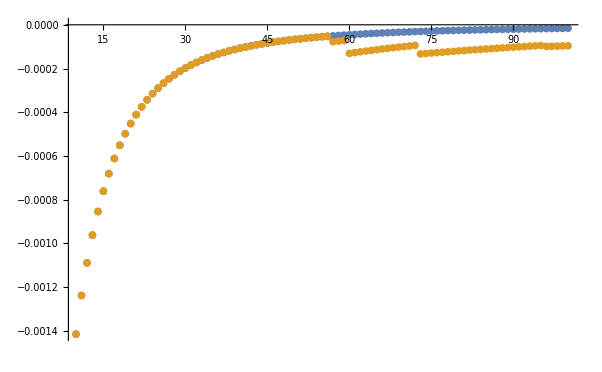

```mathematica
ListPlot[{Quiet[ParallelTable[{a,gold[a,15/100,αcont[[1]],155/1000]},{a,10,100,1}]],Quiet[ParallelTable[{a,gImAn[a,15/100,1/1000000,αcont[[1]],155/1000]},{a,10,100,1}]]},PlotRange->All]
```

## Construct ImVs

#### Wronskian

```mathematica
N[Wronskian[{ParabolicCylinderD[-1/2,√2 x μ],ParabolicCylinderD[-1/2,ⅈ √2 x μ]},x]/.{x->10^7,μ->5}]
```

5.-5. ⅈ

### Solution

```mathematica
ImVs[r_,mD_,α_,σ_]:=-Re[ParabolicCylinderD[-1/2,ⅈ √2(mD^2 σ/α)^(1/4) r]]Quiet[NIntegrate[(ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4) s] s^2 gImAnInter[s])/((mD^2 σ/α)^(1/4)),{s,r,10^5},MaxRecursion->20,WorkingPrecision->10]]-ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)r]Quiet[NIntegrate[(Re[ParabolicCylinderD[-1/2,ⅈ √2(mD^2 σ/α)^(1/4) s]] s^2 gImAnInter[s])/((mD^2 σ/α)^(1/4)),{s,0,r},MaxRecursion->20,WorkingPrecision->10]];
```

#### Plots for v=0.5,mD=0.15

```mathematica
(*evaluation for these parameters*)
```

```mathematica
Block[{v=1/2,mD=15/100,α=αcont[[1]],T=155/1000},gImAnTab=Join[ParallelTable[{r,gImAn[r,mD,v,α,T]},{r,10^-10,10^-5,10^-10}],ParallelTable[{r,gImAn[r,mD,v,α,T]},{r,2 10^-5,10^-1,10^-5}],ParallelTable[{r,gImAn[r,mD,v,α,T]},{r,2 10^-1,100,10^-1}],ParallelTable[{r,gImAn[r,mD,v,α,T]},{r,101,10^3,1}]]]//AbsoluteTiming;
```

```mathematica
gImAnInter=Interpolation[gImAnTab];
```

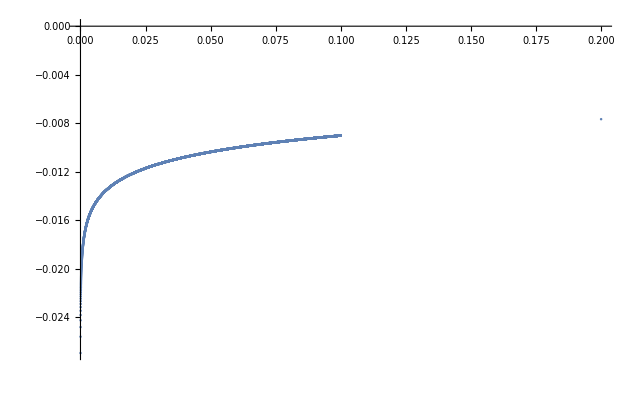

```mathematica
ListPlot[gImAnTab[[100000;;110000]],PlotRange->All]
```

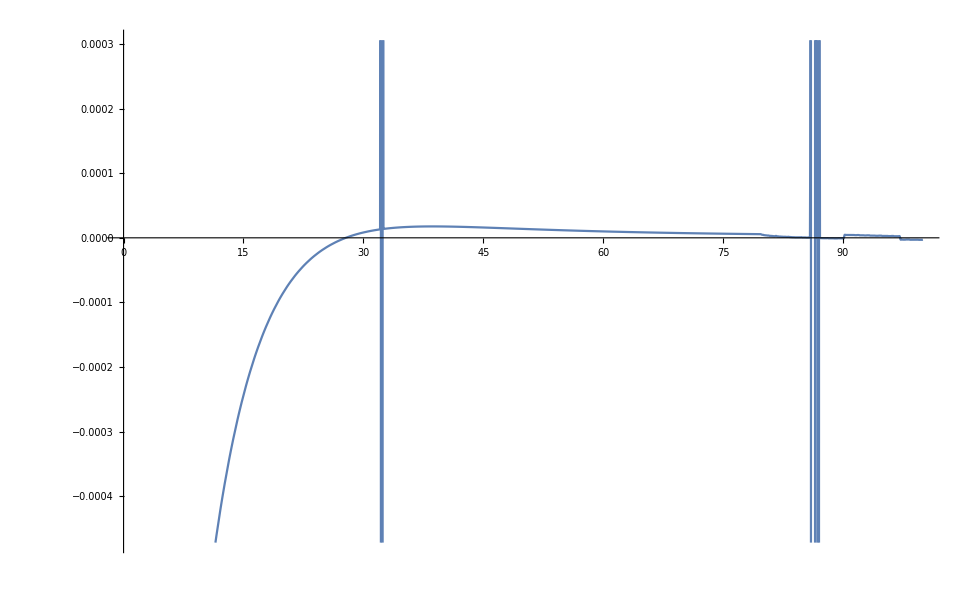

```mathematica
Plot[gImAnInter[x],{x,10^-10,100}]
```

```mathematica
ImVsTab=ParallelTable[{r,ImVs[r,15/100,αcont[[1]],σcont[[1]]]},{r,10^-10,100,1/10}];
```

```mathematica
ImVsInter=Interpolation[ImVsTab];
```

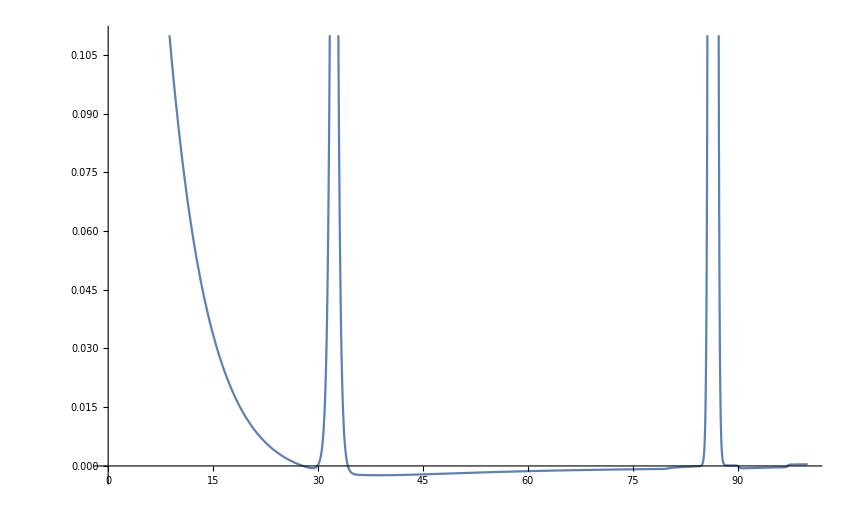

```mathematica
Plot[ImVsInter[r],{r,10^-10,100}]
```

#### Check that ImVs[m -> 0] ->0

#### Check that ImVs[v -> 0] ->ImVsold

```mathematica
ImVsold[r_,mD_,α_,σ_]:=-Re[ParabolicCylinderD[-1/2,ⅈ √2(mD^2 σ/α)^(1/4) r]]Quiet[NIntegrate[(ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4) s] s^2 gold[s])/((mD^2 σ/α)^(1/4)),{s,r,10^5},MaxRecursion->20,WorkingPrecision->10]]-ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)r]Quiet[NIntegrate[(Re[ParabolicCylinderD[-1/2,ⅈ √2(mD^2 σ/α)^(1/4) s]] s^2 gold[s])/((mD^2 σ/α)^(1/4)),{s,0,r},MaxRecursion->20,WorkingPrecision->10]];
```

```mathematica
Plot[ImVsold[r,15/100,αcont[[1]],σcont[[1]]],{r,0,20},PlotRange->All]
```

-Graphics-